{1->7,1->3,2->1,2->5,3->6,3->4,4->7,5->1,5->3,5->4,6->5,7->3,7->5}

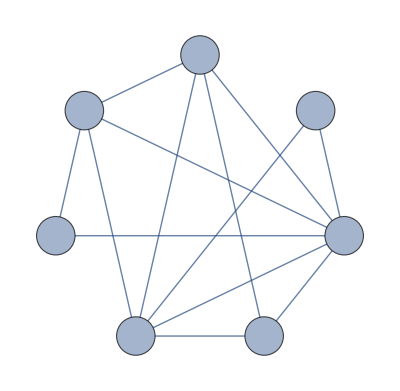

{x_(1->3)+x_(1->7)-x_(2->1)-x_(5->1),x_(2->1)+x_(2->5),-x_(1->3)+x_(3->4)+x_(3->6)-x_(5->3)-x_(7->3),-x_(3->4)+x_(4->7)-x_(5->4),-x_(2->5)+x_(5->1)+x_(5->3)+x_(5->4)-x_(6->5)-x_(7->5),-x_(3->6)+x_(6->5),-x_(1->7)-x_(4->7)+x_(7->3)+x_(7->5)}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x_(2->5)→4-x_(2->1),x_(5->1)→-7+x_(1->3)+x_(1->7)-x_(2->1),x_(5->4)→7-x_(3->4)+x_(4->7),x_(6->5)→-1+x_(3->6),x_(7->3)→1-x_(1->3)+x_(3->4)+x_(3->6)-x_(5->3),x_(7->5)→-1+x_(1->3)+x_(1->7)-x_(3->4)-x_(3->6)+x_(4->7)+x_(5->3)}}

{True}

```mathematica
inFileName=StringJoin[{NotebookDirectory[],"input.txt"}];
fileStream=OpenRead[inFileName];
vertex=Read[fileStream, {Word,Number}][[2]];
edge=Read[fileStream, {Word,Number}][[2]];
edges=ReadList[fileStream,Expression,edge];
array=Array[0&,vertex];
listInput=ReadList[fileStream,String];
For[i=1,i≤vertex,i++,array[[i]]=ToExpression[StringSplit[listInput[[i]],{"b","_","/*","*/"}]][[2]]];

verticesList=Array[#&,vertex];
edgesList=Table[edges[[i,1]]->edges[[i,2]],{i,edge}]
Close[fileStream];
graph=Graph[verticesList,edgesList, GraphLayout->"CircularEmbedding", VertexSize->0.3, VertexLabels->Placed["Name", Center], VertexLabelStyle->Directive[Bold,Italic,20],EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.05]]
equations=Array[0&,vertex];
vars=Array[0&,edge];
vars = Subscript[x,#]&/@edgesList;
(*For[i=1,i≤ edge,i++,equations[[edges[[i,1]]]]=equations[[edges[[i,1]]]]+Subscript[x,edges[[i,1]]->  edges[[i,2]]];equations[[edges[[i,2]]]]=equations[[edges[[i,2]]]]-Subscript[x,edges[[i,1]]-> edges[[i,2]]];
vars[[i]]=Subscript[x,edges[[i,1]]->  edges[[i,2]]]];*)


equations = Total/@(Subscript[x,#]&/@Cases[edgesList,#->_]&)/@verticesList- Total/@(Subscript[x,#]&/@Cases[edgesList,_->#]&)/@verticesList
Solve[equations==array,vars]
equations==array/.%//Simplify
```

```mathematica
="="({{Subscript[x, 1->3]+Subscript[x, 1->7]-Subscript[x, 2->1]-Subscript[x, 5->1]}, {Subscript[x, 2->1]+Subscript[x, 2->5]}, {-Subscript[x, 1->3]+Subscript[x, 3->4]+Subscript[x, 3->6]-Subscript[x, 5->3]-Subscript[x, 7->3]}, {-Subscript[x, 3->4]+Subscript[x, 4->7]-Subscript[x, 5->4]}, {-Subscript[x, 2->5]+Subscript[x, 5->1]+Subscript[x, 5->3]+Subscript[x, 5->4]-Subscript[x, 6->5]-Subscript[x, 7->5]}, {-Subscript[x, 3->6]+Subscript[x, 6->5]}, {-Subscript[x, 1->7]-Subscript[x, 4->7]+Subscript[x, 7->3]+Subscript[x, 7->5]}})({{7}, {4}, {-1}, {-7}, {-2}, {-1}, {0}})
```

=={x_(1->3)+x_(1->7)-x_(2->1)-x_(5->1),x_(2->1)+x_(2->5),-x_(1->3)+x_(3->4)+x_(3->6)-x_(5->3)-x_(7->3),-x_(3->4)+x_(4->7)-x_(5->4),-x_(2->5)+x_(5->1)+x_(5->3)+x_(5->4)-x_(6->5)-x_(7->5),-x_(3->6)+x_(6->5),-x_(1->7)-x_(4->7)+x_(7->3)+x_(7->5)}{7,4,-1,-7,-2,-1,0}